# Fourier Series Example

## Physics 17 (Spring 2022, Lecture 18) Prof. Flip Tanedo

## Background

Consider the interval from zero to one with Dirichlet boundary conditions. The Fourier basis functions are

ξ_n[x] =√2 Sin[k_n x]
k_n= n π

Let’s define such a basis and test orthonormality:

```mathematica
ξ[x_,n_]:=√2 Sin[n π x]
Integrate[ξ[x,1]ξ[x,2],{x,0,1}]
Integrate[ξ[x,4]ξ[x,4],{x,0,1}]
```

0

1

## Inner Product

The inner product between a function and one of the Fourier basis functions is:

<ξ_n,f> = ∫ξ_n(x) f(x)ⅆx

Let’s define a function that does this: 
(Mathematica has its own function for this, but let’s do everything “low level”)

```mathematica
Cn[n_,f_]:=∫_0^1 ξ[x,n] f[x]ⅆx
```

Let’s test this:

```mathematica
testfunction[x_]:=√2 Sin[3 π x]
Cn[3,testfunction]
Cn[2,testfunction]
```

1

0

## Fourier Series

The expansion of a function in terms of the Fourier modes is:

f[x]= ∑_(n=1)^∞ |ξ_n><ξ_n| f> =∑_(n=1)^∞ <ξ_n,f> ξ_n(x)

Observe  that the key step was inserting the unit matrix:

1 = ∑_(n=1)^∞ |ξ_n><ξ_n|

## Example

Consider the following function

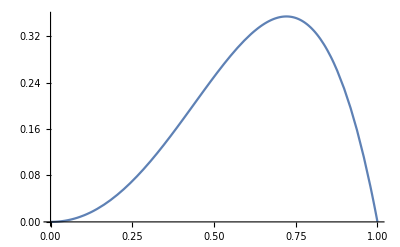

```mathematica
f[x_]:=-x^2(x-1)(1+2x)
Plot[f[x],{x,0,1}]
```

Let’s see what the first few Fourier coefficients are:

```mathematica
C1=Cn[1,f]
C2=Cn[2,f]
C3=Cn[3,f]
```

(2 √2 (-48+7 π^2))/π^5

-9/(2 √2 π^3)

(2 √2 (-16+21 π^2))/(81 π^5)

Now we can go ahead and plot the Fourier approximation for different number of modes:

```mathematica
f1[x_]:=C1 ξ[x,1]
f2[x_]:=C1 ξ[x,1]+C2 ξ[x,2]
f3[x_]:=C1 ξ[x,1]+C2 ξ[x,2]+C3 ξ[x,3]
```

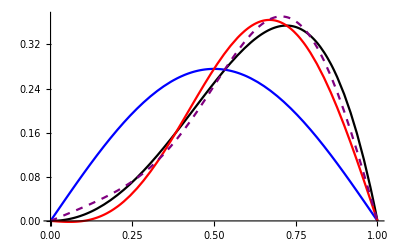

```mathematica
Plot[
{f[x],
f1[x],
f2[x],
f3[x]},
{x,0,1},
PlotStyle->{Black, Blue, Red,{Purple,Dashed}}
]
```